```mathematica
Problem 1
A cake with three regions has to be divided among two people with values: 
19 0 81
0 20 80
We can find a sum-maximizing division with this command:
```

```mathematica
FindMaximum[{(81x+19)+(80(1-x)+20),0≤x≤1},x]
```

{120.,{x→1.}}

To maximize the sum of roots we would do:

```mathematica
FindMaximum[{(81x+19)^0.5+(80(1-x)+20)^0.5,0≤x≤1},x]
```

{15.4601,{x→0.512327}}

To maximize the product of values - which gives an envy-free allocation - we do:

```mathematica
FindMaximum[{Log[81x+19]+Log[80(1-x)+20],0≤x≤1},x]
```

{8.18043,{x→0.507716}}

```mathematica
Problem 2
```

A cake with four regions has to be divided among 3 people with values: 
19 0 0 81
0 20 0 80
0 0 40 60
We can find a product-maximizing division with this command:

```mathematica
Welfare[x_,y_,z_]:=Log[81x+19]+Log[80 y+20]+Log[60z+40]
```

```mathematica
FindMaximum[{Welfare[x,y,z],0<=x<=1, 0<=y<=1,0<=z<=1, x+y+z==1},{x,y,z}]
```

{11.8731,{x→0.48251,y→0.467078,z→0.0504124}}

```mathematica
Or with this command:
```

```mathematica
Welfare2[x_,y_] := Welfare[x,y,1-x-y]
```

```mathematica
FindMaximum[{Welfare2[x,y],0<=x<=1,0<=y<=1,0<=x+y<=1},{{x,0},{y,0}}]
```

{11.8731,{x→0.48251,y→0.467078}}

Here is the optimal solution in a plot:

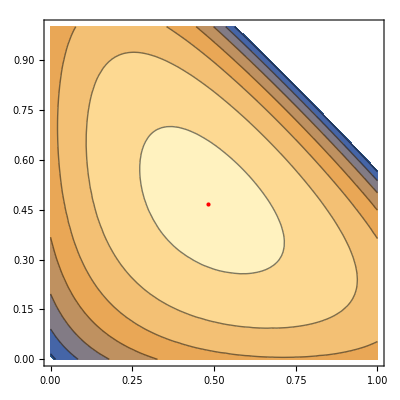

```mathematica
Show[ContourPlot[Welfare2[x,y],{x,0,1},{y,0,1}],Graphics[{Red,PointSize[Large],Point[{x,y}/.Last[%]]}]]
```

NMaximize calculates a global maximum. In this case it is identical to the local maximum of FindMaximum:

```mathematica
NMaximize[{Welfare2[x,y],0<=x<=1,0<=y<=1,0<=x+y<=1},{x,y}]
```

{11.8731,{x→0.48251,y→0.467078}}

```mathematica
Now, let's try to do the same with DISCRETE variables (i.e, the items are indivisible).
```

```mathematica
FindMaximum[{Log[81x+19]+Log[80 y+20]+Log[60z+40],0<=x<=1, 0<=y<=1,0<=z<=1, x+y+z==1, Element[{x,y,z},Integers]},{x,y,z}]
```

FindMaximum::eqineq: Constraints in {(x|y|z)∈,x+y+z==1,0≤x,0≤y,0≤z,x≤1,y≤1,z≤1} are not all equality or inequality constraints. With the exception of integer domain constraints for linear programming, domain constraints or constraints with Unequal (!=) are not supported.

FindMaximum[{Log[81 x+19]+Log[80 y+20]+Log[60 z+40],0≤x≤1,0≤y≤1,0≤z≤1,x+y+z==1,{x,y,z}∈ℤ},{x,y,z}]

```mathematica
This does not work, because the welfare function is not linear!

Non-linear problems with integers are very hard, even for Mathematica!

The trick is to find a linear approximation to this problem.

We start with a different problem that is still non-linear. 
We first try it with continuous variables to ensure it is equivalent to the previous one:
```

```mathematica
FindMaximum[{W1+W2+W3,W1≤ Log[81x+19],  W2≤ Log[80 y+20], W3≤ Log[60z+40],0<=x<=1, 0<=y<=1,0<=z<=1, x+y+z==1},{W1,W2,W3,x,y,z}]
```

{11.8731,{W1→4.06188,W2→4.04946,W3→3.76178,x→0.48251,y→0.467078,z→0.0504124}}

```mathematica
It still does not work with integrality constraints:
```

```mathematica
FindMaximum[{W1+W2+W3,
W1≤ Log[81x+19], 
 W2≤ Log[80 y+20], 
W3≤ Log[60z+40],
0<=x<=1, 0<=y<=1,0<=z<=1, x+y+z==1, Element[{x,y,z},Integers]},{W1,W2,W3,x,y,z}]
```

FindMaximum::eqineq: Constraints in {(x|y|z)∈,x+y+z==1,0≤x,0≤y,0≤z,W1≤Log[19+81 x],W2≤Log[20+80 y],W3≤Log[40+60 z],x≤1,y≤1,z≤1} are not all equality or inequality constraints. With the exception of integer domain constraints for linear programming, domain constraints or constraints with Unequal (!=) are not supported.

FindMaximum[{W1+W2+W3,W1≤Log[81 x+19],W2≤Log[80 y+20],W3≤Log[60 z+40],0≤x≤1,0≤y≤1,0≤z≤1,x+y+z==1,{x,y,z}∈ℤ},{W1,W2,W3,x,y,z}]

```mathematica
FindMaximum[{W1+W2+W3,
W1≤ Log[1]+(Log[2]-Log[1])*(81x+19-1),
W1≤ Log[2]+(Log[3]-Log[2])*(81x+19-2),
W1≤ Log[3]+(Log[4]-Log[3])*(81x+19-3),
W1≤ Log[4]+(Log[5]-Log[4])*(81x+19-4),
W1≤ Log[5]+(Log[6]-Log[5])*(81x+19-5),
W1≤ Log[6]+(Log[7]-Log[6])*(81x+19-6),
W2≤ Log[1] + (Log[2]-Log[1])*(80 y+20-1), 
W2≤ Log[2] + (Log[3]-Log[2])*(80 y+20-2), 
W2≤ Log[3] + (Log[4]-Log[3])*(80 y+20-3), 
W2≤ Log[4] + (Log[5]-Log[4])*(80 y+20-4), 
W2≤ Log[5] + (Log[6]-Log[5])*(80 y+20-5), 
W2≤ Log[6] + (Log[7]-Log[6])*(80 y+20-6), 
W3≤ Log[1] + (Log[2]-Log[1])*(60z+40-1), 
W3≤ Log[2] + (Log[3]-Log[2])*(60z+40-2), 
W3≤ Log[3] + (Log[4]-Log[3])*(60z+40-3), 
W3≤ Log[4] + (Log[5]-Log[4])*(60z+40-4), 
W3≤ Log[5] + (Log[6]-Log[5])*(60z+40-5), 
W3≤ Log[6] + (Log[7]-Log[6])*(60z+40-6), 
0<=x<=1, 0<=y<=1,0<=z<=1, x+y+z==1, Element[{x,y,z},Integers]},{W1,W2,W3,x,y,z}]
```

{27.2647,{W1→16.2819,W2→3.94987,W3→7.03288,x→1,y→0,z→0}}

```mathematica
Now there is a solution - it says that the first agent should get the fourth item. This indeed maximizes the product  of values.
```

```mathematica
.13
```